# Подкаст 1 “Галопом по Европе”

## Числа

```mathematica
1+1
```

```mathematica
12345678910 * 1234567
```

```mathematica
((1+1) * 2 + 1)*3+1
```

```mathematica
23/37
```

```mathematica
N[23/37]
```

```mathematica
N[23/37,100]
```

```mathematica
In[6]
```

```mathematica
12/36
```

```mathematica
3^2
```

```mathematica
3^2
```

```mathematica
5^(5^5)
```

```mathematica
13.1 + 2/3
```

```mathematica
Pi
```

```mathematica
N[Pi,100]
```

```mathematica
I
```

```mathematica
(1+I)^2
```

```mathematica
I^2
```

## Функции

```mathematica
Sqrt[4]
```

```mathematica
Sin[Pi/4]
```

```mathematica
Pi
```

```mathematica
f[x_]:=x^2+1
```

```mathematica
f[10]
```

```mathematica
f[x_]:=Module[
{t},
t = x^2;
(t+1)/t
]
```

```mathematica
f[2]
```

```mathematica
f[a]
```

```mathematica
{1,1,2,3,5,8,13 }
```

```mathematica
Fib[n_]:=If[n==1 || n==0, 1, Fib[n-1]+Fib[n-2]];
```

```mathematica
Fib[10]
```

```mathematica
g=(#+2)&
```

```mathematica
g[3]
```

```mathematica
3//g
```

```mathematica
g[3]
```

```mathematica
Range[20]
```

```mathematica
Fib/@Range[25]//Timing
```

```mathematica
Fib[m]
```

```mathematica
FibX[x_,n_]:=If[n==0,1,1+x/FibX[x,n-1]]
```

```mathematica
FibX[x,5]
```

```mathematica
ap[n_]:=2n+a;bp[n_]:=n^2+b;
PCF[{a_,b_},n0_, n_]:=If[n==n0, 0,bp[n0]/(ap[n0]+PCF[{a,b},n0+1,n]) ];
```

```mathematica
PCF[{a,b},1,6]
```

```mathematica
PCF[12,1,6]
```

```mathematica
FullSimplify[FibX[x,10]]
```

## Графики (data visualisation)

```mathematica
Plot[x^2,{x,-3,3}, GridLines->Automatic]
```

```mathematica
SetOptions[{Plot},GridLines->Automatic];
```

```mathematica
Plot[(x-1)(x-2)(x-3)(x-4),{x,0,5}]
```

```mathematica
Clear[f,g];
f[x_]:=1/(1+Exp[-x]); g[x_]:=Exp[x];
Plot[{f[x],g[x]},{x,-3,1}]
```

```mathematica
Manipulate[
Plot[Sin[a x]/ x,{x,-10,10}],
{{a,1},-5,5}
]
```

```mathematica
Manipulate[
Plot[{Sin[a x]/ x,Sin[a x],1/x},{x,-10,10}, PlotRange->{Automatic,{-4,4}}],
{{a,1},-5,5}
]
```

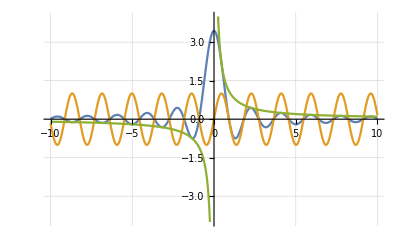

```mathematica
ap[n_]:=a n+1;bp[n_]:=n(n-b);
PCF[{a_,b_},n0_, n_]:=If[n==n0, 0,bp[n0]/(ap[n0]+PCF[{a,b},n0+1,n]) ];
expr=PCF[{a,b},1, 6]
```

```mathematica
SetOptions[{Plot,DensityPlot, ListPlot,LogPlot,ListLogPlot, RegionPlot},GridLines->Automatic];
```

```mathematica
RegionPlot[{x+y<5,x+y-5 < 2Sin[Pi (x-y)] && x+y>5 },{x,-0,6},{y,0,5},PlotPoints->50 ]
```

```mathematica
Soft[y_]:=If[y>0, Log[y],Log[-y]];
DensityPlot[Soft[Abs[expr-Pi/2]],{a,-15,15},{b,-1,45},PlotPoints->150,GridLines->Automatic]
```

```mathematica
RegionPlot3D[
-4 a^5 b^2-27 a^2 b^4+16 a^6 c+144 a^3 b^2 c-128 a^4 c^2+256 a^2 c^3 >0,
{a,-15,15},
{b,-15,15},
{c,-15,15},
PlotPoints->200,AxesLabel->{"a","b","c"}
]
```

## Уравнения

```mathematica
Solve[{x + 3y == 10, x -y == 2},{x,y}]
```

```mathematica
Solve[x^2-3x +1==0,x]
```

```mathematica
Solve[x^2-3x +5==0,x]
```

```mathematica
I
```

```mathematica
I^2
```

```mathematica
Solve[Sin[x]==2,x]
```

```mathematica
ArcSin[2]
```

```mathematica
ComplexExpand[ArcSin[2]]
```

```mathematica
Solve[{x^2==y+1,y^3==x-1},{x,y}]
```

```mathematica
Solve[x^4+3 x^2- x-12==0,x]
```

```mathematica
Solve[x^4+Pi  x^2- x-12==0,x,Quartics->True][[1]]
```

```mathematica
NSolve[x^4+3 x^2- x-12==0,x]
```

```mathematica
expr
```

```mathematica
expr=PCF[{a,b},1,3]
```

```mathematica
Solve[expr==Pi/2,{a,b}]
```

## Ряды

```mathematica
Sum[1/n^2,{n, 1,∞}]
```

```mathematica
∑_(n=1)^∞ 1/n^2
```

```mathematica
Sum[h[n],{n, 1,∞}]
```

```mathematica
∑_(n=1)^∞ 1/(n (n+1)(n+2))
```

```mathematica
∑_(n=1)^∞ 1/(n^2(n+1))
```

```mathematica
∑_(n=1)^∞ 2^-n/(n^2(n+1))
```

```mathematica
∑_(n=1)^10 2^-n/(n^2(n+1))
```

## Численные ряды

```mathematica
EulerPhi[12] (* 12 |≢ 1, 3, 5, 7, *)
```

```mathematica
EulerPhi[7] (* 7 |≢ 1,2,3,4,5,6 *)
```

```mathematica
EulerPhi[15] (* 8 |=  1,2,4,7,8,11,13,14*)
```

```mathematica
Range[10]
```

```mathematica
Sin[Range[5]]
```

```mathematica
Thread[FF[Range[10]]]
```

```mathematica
EulerPhi[Range[10]]
```

```mathematica
Clear[a,b,c,d];Accumulate[{a,b,c,d}]
```

```mathematica
Accumulate[EulerPhi[Range[10]]]
```

```mathematica
l1=Accumulate[EulerPhi[Range[100]]]
```

```mathematica
ListPlot[l1]
```

```mathematica
Plus@@{a,b,c,d}
```

```mathematica
Plus@@(EulerPhi[Range[1000]])/1000^2
```

```mathematica
N[Plus@@(EulerPhi[Range[1000]])/1000^2]
```

```mathematica
N[Plus@@(EulerPhi[Range[10000]])/10000^2]
```

```mathematica
3.0/Pi^2
```

```mathematica
{a,b,c,d}-{1,2,3,4}
```

```mathematica
n=1000;
ListPlot[Accumulate[EulerPhi[Range[n]]] - 3/Pi^2 Range[n]^2 ]
```

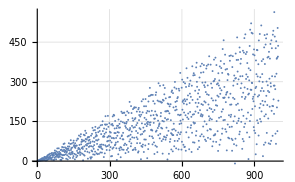

```mathematica
Range[10]^2
```

```mathematica
0.1 Range[10]
```

```mathematica
n=1000;
ListPlot[Accumulate[EulerPhi[Range[n]]] - 3/Pi^2 Range[n]^2 -0.2 Range[n]]
```

```mathematica
n=1000;
ListPlot[Accumulate[EulerPhi[Range[n]]] - 3/Pi^2 Range[n]^2 - 3/Pi^2 Range[n]]
```

```mathematica
Range[10] * 1/Range[10]
```

```mathematica
n=10000;
l=N[(Accumulate[EulerPhi[Range[n]]] - 3/Pi^2 Range[n]^2 - 3/Pi^2 Range[n])*1/Range[n]];
```

```mathematica
ListPlot[l]
```

```mathematica
Histogram[l,{0.02}]
```

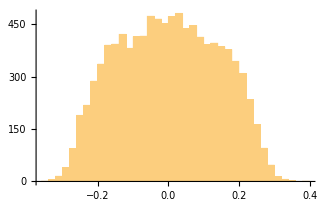

## Таблицы

```mathematica
Table[n^2,{n,1,10}]
```

```mathematica
Range[10]^2
```

```mathematica
Table[a*b,{a,1,10},{b,1,10}]
```

```mathematica
Grid[Table[a*b,{a,1,10},{b,1,10}]]
```

```mathematica
n=13;
Grid[Table[Mod[a*b,n],{a,1,n-1},{b,1,n-1}],Frame->True]
```

```mathematica
Manipulate[
ArrayPlot[Table[Mod[a*b,n],{a,1,n-1},{b,1,n-1}],Frame->True],
{{n,13},1,1000,1}
]
```

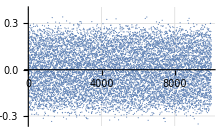
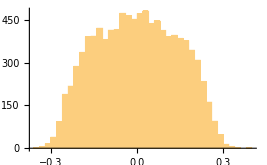
```mathematica
-Graphics--Graphics--Graphics-
```

## Пполиномы

```mathematica
Zeta[2]
```

```mathematica
BernoulliB[6,x]
```

```mathematica
ChebyshevT[6,x]
```

```mathematica
EulerE[6,x]
```

```mathematica
sol=NSolve[BernoulliB[60,x]]
```

```mathematica
x/.sol
```

```mathematica
CPoint[z_]:={Re[z],Im[z]};
```

```mathematica
CPoint[x/.sol]
```

```mathematica
Transpose[CPoint[x/.sol]]
```

```mathematica
ListPlot[Transpose[CPoint[x/.sol]], AspectRatio->1]
```

```mathematica
ListPlot[Transpose[CPoint[x/.Solve[BernoulliB[200,x]==0,x]]]]
```

## Моделирование

```mathematica
Evolve[{tS0_, tI0_, tR0_},{transRate_, recovRate_},steps_,deltaT_ ]:=Module[
{
 tS, tI, tR,
deltaS, deltaI, deltaR
},

{tS, tI, tR} = {tS0, tI0, tR0};

(
{tS, tI, tR}/=tS + tI + tR;
deltaS = - transRate tS tI;
deltaI = transRate tS tI - recovRate tI;
deltaR = recovRate tI;
{tS, tI, tR} += {deltaS, deltaI, deltaR}*deltaT;
{tS, tI, tR}
)&/@Range[steps]
];
```

```mathematica
x0={0.99, 0.01, 0};
```

```mathematica
{transRate, recovRate}={3.2, 0.23};
steps=10;
deltaT=0.1;
Evolve[x0,{transRate, recovRate},steps, deltaT]
```

```mathematica
Manipulate[
data=Evolve[x0,{transRate, recovRate},steps, Exp[deltaTLog]];
ListPlot[Evaluate[Transpose[data]],Joined->True, GridLines->Automatic, PlotRange->{Automatic, {0,1}}, PlotLabel->"R0="<>ToString[transRate/recovRate]],
{{transRate, 0.42}, 0, 1},
{{recovRate, 0.13}, 0, 1},
{{deltaTLog,-2},-5,0 },
{{steps,300},10,10000}
]
```